```mathematica
g = 9.81; (* gravitational constant *)
v0 = 30;  (* initial velocity of the ball, about 100 km/h *)
theta = Pi/4; (* initial angle, optimal for zero drag *)
k = 0.03; (* drag coefficient of a baseball *)
```

```mathematica
traj1 = NDSolve [ 
{ 
x''[t] == -k x'[t]Sqrt[y'[t]^2 + x'[t]^2] , y''[t] == -k y'[t]Sqrt[y'[t]^2 + x'[t]^2] -g,
x[0] == 0, 
y[0] == 0, 
x'[0] == v0 Cos[theta],
y'[0] == v0 Sin[theta] 
}, 
{x, y}, {t, 0, 10}]
```

{{x→InterpolatingFunction[{{0.,10.}},<>],y→InterpolatingFunction[{{0.,10.}},<>]}}

```mathematica
traj2 = NDSolve [ 
{ 
x''[t] == -k x'[t]Sqrt[y'[t]^2 + x'[t]^2] , y''[t] == -k y'[t]Sqrt[y'[t]^2 + x'[t]^2] -g,
x[0] == 0, 
y[0] == 3, 
x'[0] == v0 Cos[theta],
y'[0] == v0 Sin[theta] 
}, 
{x, y}, {t, 0, 10}]
```

{{x→InterpolatingFunction[{{0.,10.}},<>],y→InterpolatingFunction[{{0.,10.}},<>]}}

```mathematica
tflight1 =t/. FindRoot[y[t] /. Flatten[traj1], {t, 0.1, 10}]
```

3.11558

```mathematica
tflight2 =t/. FindRoot[y[t] /. Flatten[traj2], {t, 0.1, 10}]
```

3.34504

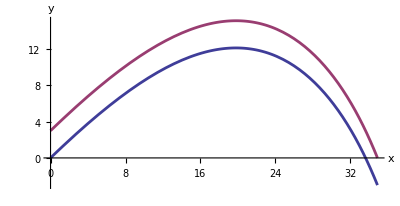

```mathematica
p1 = ParametricPlot[{
Evaluate[{x[t], y[t]}/.traj1],
Evaluate[{x[t], y[t]}/.traj2]},
{t, 0, tflight2},
AxesLabel -> {"x", "y"},
PlotStyle -> {AbsoluteThickness[2]}
]
```

```mathematica
tof[theta_]:=Module[{traj, tflight},
traj = NDSolve [ 
{ 
x''[t] == -k x'[t]Sqrt[y'[t]^2 + x'[t]^2] , y''[t] == -k y'[t]Sqrt[y'[t]^2 + x'[t]^2] -g,
x[0] == 0, 
y[0] == 0, 
x'[0] == v0 Cos[theta],
y'[0] == v0 Sin[theta] 
}, 
{x, y}, {t, 0, 10}];
tflight =t/. FindRoot[y[t] /. Flatten[traj], {t, 0.1, 10}];
N[tflight]
]
```

```mathematica
finalx[theta_]:= Module[{},N[v0*tof[theta]]]
```

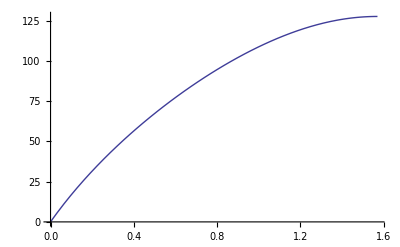

```mathematica
Plot[finalx[theta],{theta, 0, Pi/2}]
```

The optimal angle is at π/2 i.e steeper is better in the range [0, π/2].